```mathematica
t0:=0.0; P:=13.0;  κ:=1.5; Δ:=0.0; β:=4.0;α:=1;
```

```mathematica
a:=α/2 (α-ⅈ P)-1+(ⅈ κ  α)/2;
b:=α (α-ⅈ P) -2;
c:=(ⅈ Δ +κ)/(2 α);
```

```mathematica
μ:=0;
ν:=0;
ρ:=1/2 (-1+b+√((1+a-b)^2-4 c^2));
ω:=1/2 (-1+b-√((1+a-b)^2-4 c^2));
γ:=2 μ + a;
χ:=(ⅈ (P))/(4 α);
ζ:=(ⅈ (P))/(4 α);
z[t_]:=1/2 (1+ Tanh[α t+β]);
```

```mathematica
G[t1_,t2_]:=(z[t2])^(1-γ)  Hypergeometric2F1[ρ-γ+1,ω-γ+1,2-γ, z[t2]] Hypergeometric2F1[ρ,ω,ρ, z[t1]];

ϑ[t1_,t2_]:=(χ+μ) Log[z[t1]]+(ζ+ν) Log[1-z[t1]]-(χ+μ+1-γ)Log[z[t2]]-(ζ+ν+γ-ρ-ω)Log[1-z[t2]] ;

U12[t1_,t2_]:= ⅈ c (1-γ) (Gamma[ρ] Gamma[ω])/(Gamma[ρ+ω-γ+1] Gamma[γ]) (G[t1,t2]-G[t2,t1]) Exp[ϑ[t1,t2]];

Probability1[t_]:=Re[U12[t,t0]]^2+Im[U12[t,t0]]^2;
Probability1[2]
```

0.0019082

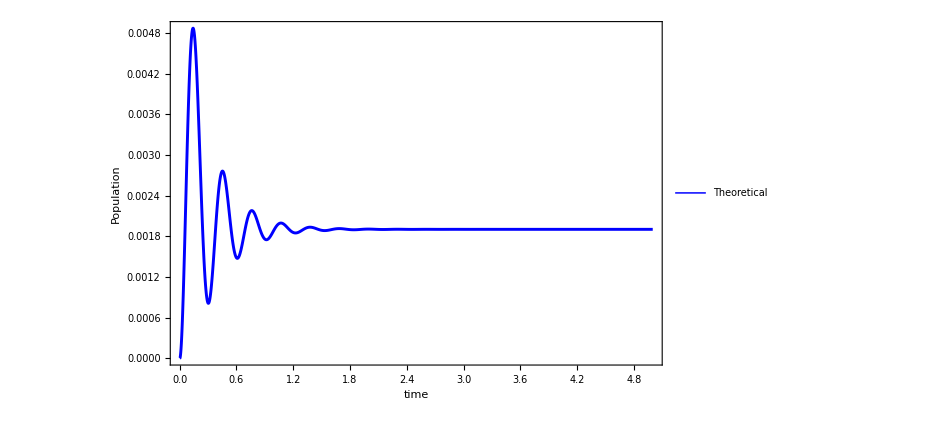

```mathematica
Np=Plot[Probability1[t],{t, 0,5},PlotRange->All,PlotStyle->{Thickness[0.003],Blue},ImageSize->700, Frame->True,Axes->None,PlotLegends->Placed[{"Theoretical"},{0.8,0.9}],LabelStyle->{FontFamily->"Times New Roman",32,GrayLevel[0.1]},FrameStyle->{{Black,Black},{Black,Black}},FrameLabel->{"time","Population","Δ = 0",""}]
```

```mathematica
t0:=0;
tfin:=5;
sol1= NDSolve[{ⅈ y1'[t]-1/2((P*Tanh[α t+β] +κ) y1[t]+(ⅈ Δ +κ) Sech[α t+β]  y2[t])==0,
                         ⅈ y2'[t]-1/2((-P*Tanh[α t+β] -κ) y2[t]+(ⅈ Δ +κ) Sech[α t+β]  y1[t])==0,
                          y1[t0]==0,y2[t0]==1},{y1,y2},{t,t0,tfin}]
```

{{y1→InterpolatingFunction[{{0., 5.}}, <>],y2→InterpolatingFunction[{{0., 5.}}, <>]}}

```mathematica
Prob1[t_]:=Re[Evaluate[y1[t]/.sol1]]^2+Im[Evaluate[y1[t]/.sol1]]^2;

Prob2[t_]:=Re[Evaluate[y2[t]/.sol1]]^2+Im[Evaluate[y2[t]/.sol1]]^2;
```

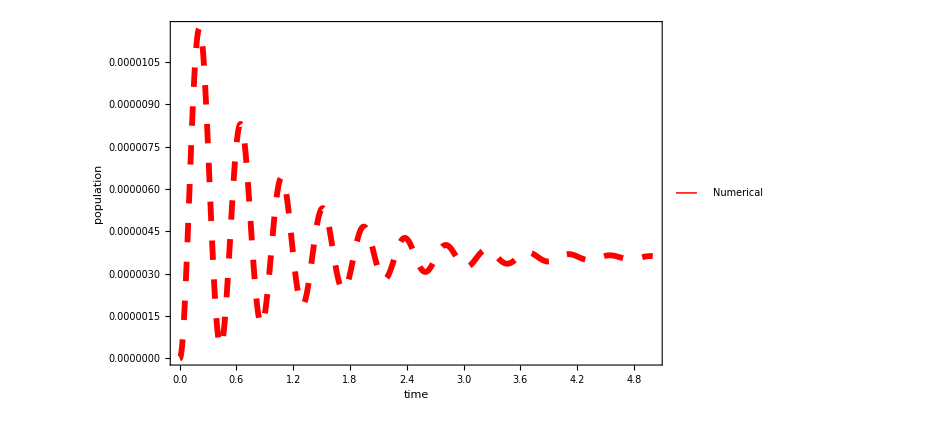

```mathematica
Mp=Plot[Prob1[t],{t,0,5},PlotRange->All,PlotStyle->{Thickness[0.006],Dashing[Large],Thickness[0.006],{Blue, Red}},PlotLegends->Placed[{"Numerical"},{0.8,0.8}],
ImageSize->700, Frame->True,Axes->None,LabelStyle->{FontFamily->"Times New Roman",32,GrayLevel[0.1]},FrameStyle->{{Black,Black},{Black,Black}},FrameLabel->{"time","population","Δ = 0"}]
```

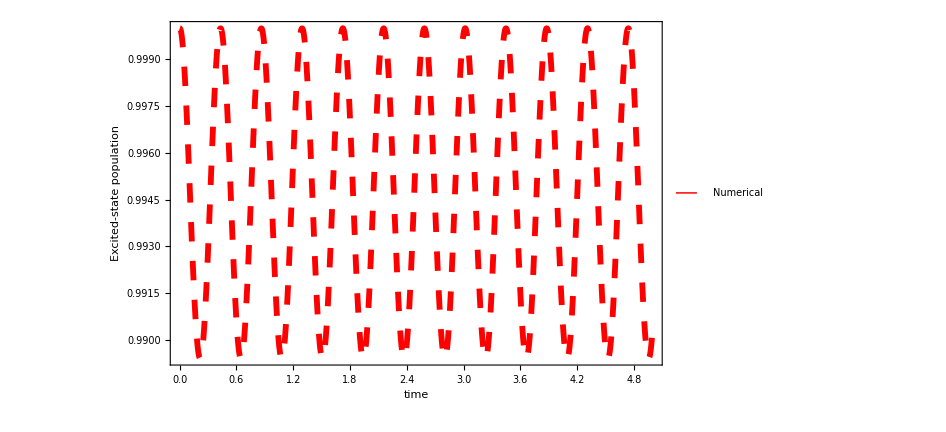

{0.991313}

```mathematica
Mp1=Plot[Prob2[t],{t,0,5},PlotRange->All,PlotStyle->{Thickness[0.006],Dashing[Large],Thickness[0.006],{Blue, Red}},PlotLegends->Placed[{"Numerical"},{0.8,0.8}],
ImageSize->700, Frame->True,Axes->None,LabelStyle->{FontFamily->"Times New Roman",32,GrayLevel[0.1]},FrameStyle->{{Black,Black},{Black,Black}},FrameLabel->{"time","Excited-state population","Δ = 0",""}]
Prob2[2]
```

```mathematica
u[t1_,t2_]:=(χ+μ+1) Log[z[t1]]+(ζ+ν+1) Log[1-z[t1]]-(χ+μ+1-γ)Log[z[t2]]-(ζ+ν+γ-ρ-ω)Log[1-z[t2]];
U22[t1_,t2_]:=-1/(1-γ)((Gamma[ρ] Gamma[ω])/(Gamma[ρ+ω-γ+1] Gamma[ γ-1]) F[t1,t2]-(Gamma[ρ] Gamma[ω] Gamma[1-γ])/(Gamma[ρ-γ+1] Gamma[ω-γ+1] Gamma[γ-1]) S[t1,t2]-s[t1])   Exp[u[t1,t2]];

Probability2[t_]:=Re[U22[t,t0]]^2+Im[U22[t,t0]]^2;
Probability2[2]
```

0.835457

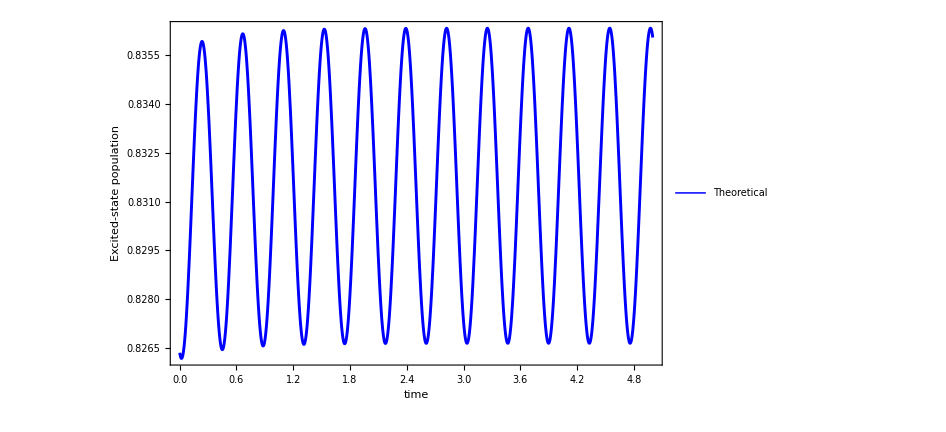

```mathematica
Np1=Plot[Probability2[t],{t, 0,5},PlotRange->All,PlotStyle->{Thickness[0.003],Blue},ImageSize->700, Frame->True,Axes->None,PlotLegends->Placed[{"Theoretical"},{0.8,0.9}],LabelStyle->{FontFamily->"Times New Roman",32,GrayLevel[0.1]},FrameStyle->{{Black,Black},{Black,Black}},FrameLabel->{"time","Excited-state population","Δ = 0",""}]
```

```mathematica
Show[Np, Mp]
```

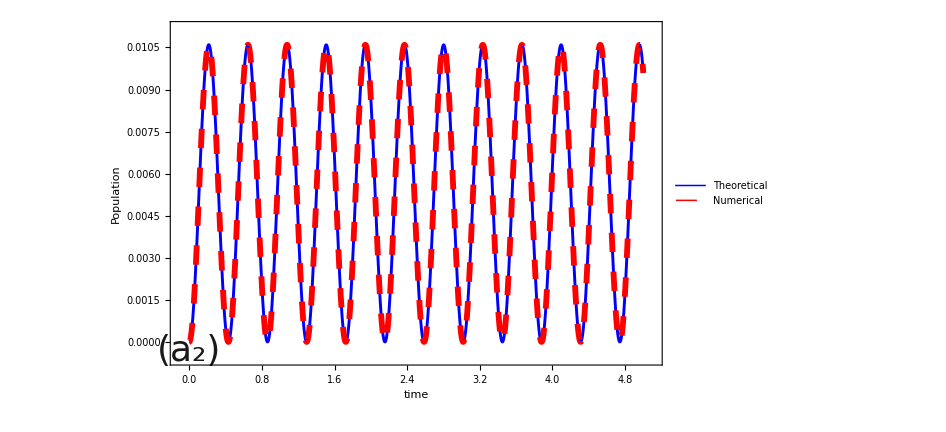

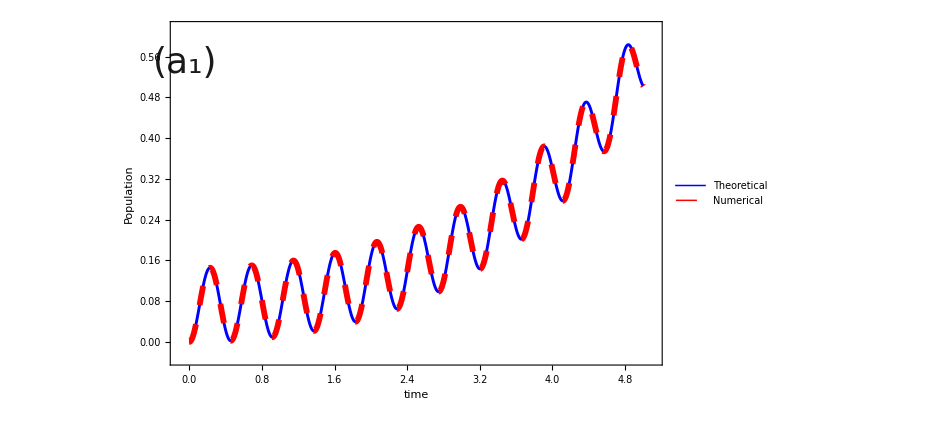

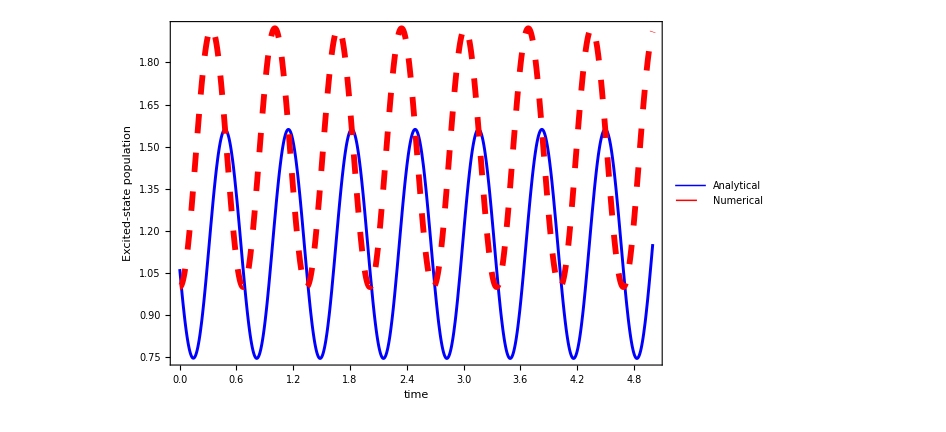

```mathematica
Show[Np1, Mp1]
```